## Pendulum swing up, robust to ω perturbations (Problem 9.2 and Section 9.1.2)

```mathematica
Clear["Global`*"];
ωnom=1;n=500;  τ=5;τ1=8;
```

Design feedforward for nominal ω = 1  (slightly modified from version in Opt. Cont. chapter)
  -- notation changed to use x1=θ, x2= θdot, λ1=λdot, λ2=λ

```mathematica
ffNom[n_,τ_]:=Module[{f,x1,x2,λ2,λ1,t,Δt,bcs,eqns,sv,froot,x1ff0,x2ff0,uff0,x1ff,x2ff,uff},
Δt=τ/n;
f[{x1_,x2_,λ1_,λ2_}] := {x2,-Sin[x1]-λ2,Cos[x1]λ2,-λ1};
bcs={Subscript[x1, 0]==0,Subscript[x2, 0]==0,Subscript[x1, n]==π,Subscript[x2, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[x1, i],Subscript[x2, i],Subscript[λ1, i],Subscript[λ2, i]}== {Subscript[x1, i-1],Subscript[x2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1]}
+Δt/2(f[{Subscript[x1, i-1],Subscript[x2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1]}]+f[{Subscript[x1, i],Subscript[x2, i],Subscript[λ1, i],Subscript[λ2, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x1, i],0},{Subscript[x2, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

x1ff0=ListInterpolation[Table[Subscript[x1, i],{i,0,n}]/.froot,{0,τ}];
x2ff0=ListInterpolation[Table[Subscript[x2, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ2, i],{i,0,n}]/.froot,{0,τ}];

x1ff[t_]:=Piecewise[{{x1ff0[t],0≤t≤τ}},π];
x2ff[t_]:=Piecewise[{{x2ff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{x1ff,x2ff,uff}]

{θnom,θdotnom,unom}=ffNom[n,τ];
```

Test the approximate solution on open-loop dynamics for different frequency ω

```mathematica
SwingUp[τ_,τ1_,uff_,ω_]:=Module[{eq,init,θ,θdot,θs,θdots,us,t,Jτ},
eq={θ'[t]==θdot[t],θdot'[t]==-ω^2 Sin[θ[t]]+uff[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
Jτ=1/2((θs[τ]-π)^2+θdots[τ]^2);
{θs,Jτ}]
```

```mathematica
GetJ[τ_,τ1_,u_,ω_]:=SwingUp[τ,τ1,u,ω][[2]]
```

```mathematica
GetJu[u_,τ_]:=1/2 NIntegrate[u[t]^2,{t,0,τ}]
```

```mathematica
GetJuNom[τ_]:=Module[{θnom,θdotnom,unom,n},n=500;{θnom,θdotnom,unom}=ffNom[n,τ];
1/2 NIntegrate[unom[t]^2,{t,0,τ}]]
```

```mathematica
GetJuRob[τ_]:=Module[{θrob,θdotrob,urob,xω1rob,xω2rob,n},n=500;{θrob,θdotrob,urob,xω1rob,xω2rob}=ffRob[n,τ];
1/2 NIntegrate[urob[t]^2,{t,0,τ}]]
```

Design robust feedforward for nominal ω = 1

```mathematica
ffRob[n_,τ_]:=Module[{f,x1,x2,xω1,xω2,λ1,λ2,λω1,λω2,t,Δt,bcs,eqns,sv,froot,x1ff0,x2ff0,uff0,xω1ff0,xω2ff0,x1ff,x2ff,uff},
Δt=τ/n;
f[{x1_,x2_,xω1_,xω2_,λ1_,λ2_,λω1_,λω2_}] := {x2,-Sin[x1]-λ2,xω2,-2Sin[x1]-Cos[x1]xω1,Cos[x1]λ2+(2Cos[x1]-Sin[x1]xω1)λω2,-λ1,Cos[x1]λω2,-λω1};
(*  GOT THIS FAR!! *)
bcs={Subscript[x1, 0]==0,Subscript[x2, 0]==0,Subscript[xω1, 0]==0,Subscript[xω2, 0]==0,Subscript[x1, n]==π,Subscript[x2, n]==0,Subscript[xω1, n]==0,Subscript[xω2, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[x1, i],Subscript[x2, i],Subscript[xω1, i],Subscript[xω2, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λω1, i],Subscript[λω2, i]}== {Subscript[x1, i-1],Subscript[x2, i-1],Subscript[xω1, i-1],Subscript[xω2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λω1, i-1],Subscript[λω2, i-1]}
+Δt/2(f[{Subscript[x1, i-1],Subscript[x2, i-1],Subscript[xω1, i-1],Subscript[xω2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λω1, i-1],Subscript[λω2, i-1]}]+f[{Subscript[x1, i],Subscript[x2, i],Subscript[xω1, i],Subscript[xω2, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λω1, i],Subscript[λω2, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x1, i],0i Δt},{Subscript[x2, i],0},{Subscript[xω1, i],0},{Subscript[xω2, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λω1, i],0},{Subscript[λω2, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

x1ff0=ListInterpolation[Table[Subscript[x1, i],{i,0,n}]/.froot,{0,τ}];
x2ff0=ListInterpolation[Table[Subscript[x2, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ2, i],{i,0,n}]/.froot,{0,τ}];
xω1ff0=ListInterpolation[Table[Subscript[xω1, i],{i,0,n}]/.froot,{0,τ}];
xω2ff0=ListInterpolation[Table[Subscript[xω2, i],{i,0,n}]/.froot,{0,τ}];

x1ff[t_]:=Piecewise[{{x1ff0[t],0≤t≤τ}},π];
x2ff[t_]:=Piecewise[{{x2ff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{x1ff,x2ff,uff,xω1ff0,xω2ff0}]

{θrob,θdotrob,urob,xω1rob,xω2rob}=ffRob[n,τ];
```

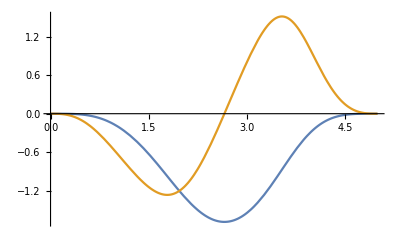

```mathematica
pω=Plot[{xω1rob[t],xω2rob[t]},{t,0,τ},PlotRange->All]
```

Evaluate nominal & robust feedforward controls u(t) for different frequencies ω

```mathematica
ϵ=0.1;
{θ1,J1}=SwingUp[τ,τ1,unom,ωnom];
{θ1a,J1a}=SwingUp[τ,τ1,unom,ωnom-ϵ];
{θ1b,J1b}=SwingUp[τ,τ1,unom,ωnom+ϵ];
Ju1=GetJu[unom,τ];

{θ2,J2}=SwingUp[τ,τ1,urob,ωnom];
{θ2a,J2a}=SwingUp[τ,τ1,urob,ωnom-ϵ];
{θ2b,J2b}=SwingUp[τ,τ1,urob,ωnom+ϵ];
Ju2=GetJu[urob,τ];
```

InterpolatingFunction::dmval: Input value {5.05981} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01349} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.06439} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.05042} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.03809} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.02222} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.04363} lies outside the range of data in the interpolating function. Extrapolation will be used.

Data for energy plots; E(τ) at end of protocol

InterpolatingFunction::dmval: Input value {5.02466} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.01092} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.0516} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.05775} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

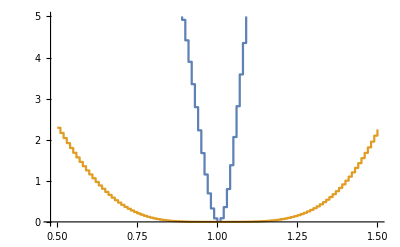

```mathematica
JdatNom=Table[GetJ[τ,τ1,unom,ω],{ω,0.5,1.5,0.01}];
JdatRob=Table[GetJ[τ,τ1,urob,ω],{ω,0.5,1.5,0.01}];
ListPlot[{JdatNom,JdatRob},DataRange->{0.5,1.5},Joined->True,PlotRange->{0,5}]
```

Graphics

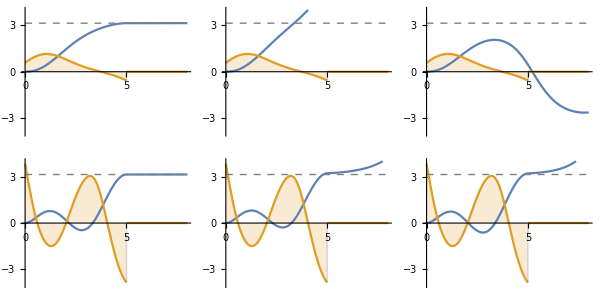

```mathematica
Plotit[θ_,u_,τ_]:= Plot[{θ[t],u[t],π},{t,0,τ},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-4,4},Filling->{2->Axis}]

p1=Plotit[θ1,unom,τ1];   (* nominal algorithm *)
p1a=Plotit[θ1a,unom,τ1];p1b=Plotit[θ1b,unom,τ1];

p2=Plotit[θ2,urob,τ1];   (* robust algorithm *)
p2a=Plotit[θ2a,urob,τ1];p2b=Plotit[θ2b,urob,τ1];

GraphicsGrid[{{p1,p1a,p1b},{p2,p2a,p2b}},Spacings->4,ImageSize->{600,300}]
```

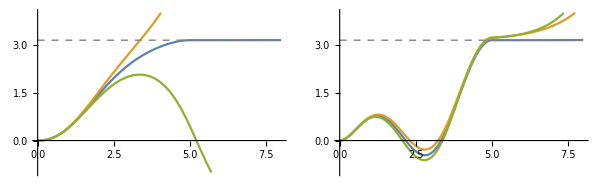
{-Graphics-,1.21261,9.87581}

```mathematica
pnom=Plot[{θ1[t],θ1a[t],θ1b[t],π},{t,0,τ1},PlotStyle->{,,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4}];
prob=Plot[{θ2[t],θ2a[t],θ2b[t],π},{t,0,τ1},PlotStyle->{,,,Directive[Gray,Dashed,Thin]},PlotRange->{-1,4}];
{GraphicsRow[{pnom,prob},Spacings->4,ImageSize->600],Ju1,Ju2}
```

```mathematica
min=3; max=10;
JudatNom=Table[GetJuNom[τ],{τ,min,max}];
JudatRob=Table[GetJuRob[τ],{τ,min,max}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

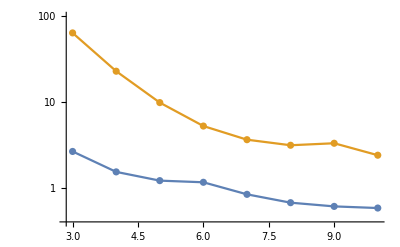

```mathematica
ListLogPlot[{JudatNom,JudatRob},DataRange->{min,max},Joined->True,Mesh->All,PlotRange->{0.4,100}]
```

Repeat for longer τ

InterpolatingFunction::dmval: Input value {10.0798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.0604} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.07} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.0779} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.0594} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.0447} lies outside the range of data in the interpolating function. Extrapolation will be used.

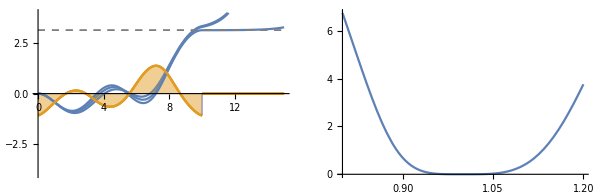
{-Graphics-,2.40149}

```mathematica
τlong=10; τ1long=1.5τlong;
{θrob1,θdotrob1,urob1,xω1rob1,xω2rob1}=ffRob[n,τlong];

ϵ1=0.05;Ju3=GetJu[urob1,τlong];
{θ3,J3}=SwingUp[τlong,τ1long,urob1,ωnom];
{θ3a,J3a}=SwingUp[τlong,τ1long,urob1,ωnom-ϵ1];
{θ3b,J3b}=SwingUp[τlong,τ1long,urob1,ωnom+ϵ1];

p3=Plotit[θ3,urob1,τ1long];   (* robust algorithm *)
p3a=Plotit[θ3a,urob1,τ1long];p3b=Plotit[θ3b,urob1,τ1long];
p3c=Plot[ GetJ[τlong,τ1long,urob1,ω],{ω,0.8,1.2}];

{GraphicsRow[{Show[p3,p3a,p3b],p3c},Spacings->4,ImageSize->600],Ju3}
```

Export data

```mathematica
dat1=Table[Through[{θ1,θ1a,θ1b,θ2,θ2a,θ2b,unom,urob}[t]],{t,0,τ1,0.05}]//N;
dat2=Table[Through[{xω1rob,xω2rob}[t]],{t,0,τ,0.05}]//N;
datJs=Transpose[{JdatNom,JdatRob}];
datJu=Transpose[{JudatNom,JudatRob}];
```

```mathematica
(* 
SetDirectory[NotebookDirectory[]];Export["pendulumPertRobust1.dat", dat1];
Export["pendulumPertRobust2.dat", dat2];
Export["pendulumPertRobustJs.dat", datJs];
Export["pendulumPertRobustJu.dat", datJu]; 
*)
```